# Two patches, with and without effects of microbes on pollinators

This creates plots of competitive outcomes (exclusion or coexistence) for yeast and bacteria across varying yeast and bacteria dispersal rates. Because yeast only disperse via pollinators and bacteria primarily disperse via non-pollinator sources, we vary parameters d_yp and d_b0.

## Load package and set working directory:

```mathematica
Needs["EcoEvo`"];
SetDirectory[NotebookDirectory[]];
SetDirectory[ParentDirectory[]<> "/_figures/_raw-nb"];
```

## Define model in EcoEvo:

```mathematica
SetModel[{Pop[Y1]->{Equation:>dy disp[B1, B2, u, L0] Y1 (1-Y1-B1)-m Y1, Range:>Interval[{0,1}], Color->RGBColor["#FFCC33"]},Pop[Y2]->{Equation:>dy disp[B2, B1, u, L0] Y2 (1-Y2-B2)-m Y2, Range:>Interval[{0,1}], Color->RGBColor["#FFCC33"], LineStyle-> Dashing[0.02]},
Pop[B1]->{Equation:>(db0+db disp[B1, B2, u, L0]) B1 (1-Y1-B1)-m B1, Range:>Interval[{0,1}], Color->RGBColor["#333399"]},
Pop[B2]->{Equation:>(db0+db disp[B2, B1, u, L0]) B2 (1-Y2-B2)-m B2, Range:>Interval[{0,1}],  Color->RGBColor["#333399"], LineStyle-> Dashing[0.02]},
Parameters:>{dy >= 0,db0 >= 0, db >= 0,u>= 0,L0>= 0,m>= 0}}];
disp[B_, Bother_, u_, L0_]:=Module[{P}, 
P = (1-B)^u/((1-B)^u+(1-Bother)^u); 
P / (L0 + P)
];
```

## Create functions used throughout and define unchanging parameter values:

```mathematica
db = 0.4;
m = 0.1;
L0 = 0.5;
SharedImageSize = 2.25 * 72; (*Image width in pts*)
(* Equilibrium yeast for varying dy, db0, and u: *)
eqYprop[par1_?NumericQ, par2_?NumericQ, par3_ ? NumericQ]:=Block[{dy = par1, db0 = par2, u = par3},
Module[{eqs, realEqs, realStableEqs, eqYprops, out},
(*
Because `SolveEcoEq[ Fixed->{Y1->0, Y2->0}]` takes so long to compute
for high values of `u`, I'm instead ignoring this scenario and
having the output for proportional yeast abundance be zero if
`eqYprops` is length zero.
*)
eqs = Join[SolveEcoEq[ Fixed->{Y1->0, B2->0} ], SolveEcoEq[ Fixed->{B1->0, B2->0} ]];
realEqs = DeleteDuplicates[Pick[eqs, (Length[Cases[Values[#], s_/;Im[s]==0]] == 4) & /@ eqs]];
realStableEqs = Pick[realEqs, EcoStableQ[realEqs]];
eqYprops = ((#[[1]] + #[[2]] )/ Total[#]) &/@ Values[realStableEqs];
out = Which[Length[eqYprops] == 0, 0.0,
Length[eqYprops] == 1, eqYprops[[1]], 
Max[eqYprops] > (1 - 10^-8), Min[eqYprops], 
Min[eqYprops] < 10^-8, Max[eqYprops]];
out]];
(* From a plot defining outcomes, get coordinates defining changes in outcomes: *)
getCoords[plot_] := Module[{tmp}, 
tmp = Cases[Normal[plot],_Line,Infinity][[1,1]];
Select[tmp, (#[[1]] > 10^-6 && #[[1]] < (2-10^-6) && #[[2]] > 10^-7 && #[[2]] < (1-10^-6)) &]
];
coexistPlot[Yplot_, Bplot_, points_] := Module[{Ycoords, Bcoords, Pplot},
Ycoords=getCoords[Yplot];
Bcoords=getCoords[Bplot];
Pplot = ListPlot[points, PlotMarkers->Graphics[{Black,Thick,Circle[]},ImageSize->10]];
Show[Yplot, Bplot, 
Graphics[{Thick, RGBColor["#008B00"], Line[Ycoords]}], 
Graphics[{Thick, RGBColor["#008B00"], Line[Bcoords]}],
Graphics[{Directive[RGBColor["#008B00"], Opacity[0.4]],
Polygon[Join[Ycoords,Bcoords]]}],
Pplot, 
ImageSize->SharedImageSize,
ImagePadding->1, (* << this removes tick labels; I'll add them in Illustrator *)
LabelStyle->None]
];
```

## Equilibria with u = 0

### Create separate plot objects:

```mathematica
Clear[dy, db0, u, fileYplotU0, YplotU0, fileBplotU0, BplotU0];

(* Save the time-consuming steps as intermediate data files and use these files if they exist. *)
fileYplotU0 = "data/Yplot-u0.mx";
fileBplotU0 = "data/Bplot-u0.mx";

If[FileExistsQ[fileYplotU0],
YplotU0=Import[fileYplotU0];, 
YplotU0 = RegionPlot[eqYprop[par1, par2, 0.0] > (1 - 10^-8),{par1,0,2},{par2,0,1}, (*PlotLabel -> "u=0",*) PlotPoints-> 5, 
BoundaryStyle-> None,
PlotStyle -> Directive[RGBColor["#FFCC33"], Opacity[0.4]]];
Export[fileYplotU0,YplotU0];];

If[FileExistsQ[fileBplotU0],
BplotU0=Import[fileBplotU0];, 
BplotU0 = RegionPlot[10^-8 > eqYprop[par1, par2, 0.0],{par1,0,2},{par2,0,1}, (*PlotLabel -> "u=0",*) PlotPoints-> 5, 
BoundaryStyle-> None,
PlotStyle -> Directive[RGBColor["#333399"], Opacity[0.4]]];
Export[fileBplotU0,BplotU0];];

UnstableLineU0 =  Graphics[{Thick, Dashed, Line[{{db, 0}, {2.0, (1/(2 * L0 + 1)) * (2.0 - db)}}]}];
```

### Combine to create final plot:

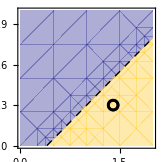

```mathematica
p = Show[BplotU0, YplotU0, UnstableLineU0,
ListPlot[{{1.4,0.3}}, PlotMarkers->Graphics[{Black,Thick,Circle[]},ImageSize->10]],
ImageSize-> SharedImageSize,
ImagePadding->1, (* << this removes tick labels; I'll add them in Illustrator *)
LabelStyle->None]
Export[File["2patch-u0-equilibria.pdf"],p, AllowRasterization->False];
Clear[p];
```

## Equilibria with u = 1

### Create separate plot objects:

```mathematica
Clear[dy, db0, u, fileYplotUlo, YplotUlo, fileBplotUlo, BplotUlo]

u=1;

(* Save the time-consuming steps as intermediate data files and use these files if they exist. *)
fileYplotUlo = "data/Yplot-u"  <> ToString[u] <> ".mx";
fileBplotUlo = "data/Bplot-u" <> ToString[u] <> ".mx";

(* Takes ~1 min if file isn't saved *)
If[FileExistsQ[fileYplotUlo],
YplotUlo = Import[fileYplotUlo];, 
YplotUlo = RegionPlot[eqYprop[par1, par2, u] > (1 - 10^-8),{par1,0,2},{par2,0,1}, 
(*PlotLabel -> "u=" <> ToString[u],*)
BoundaryStyle-> Directive[RGBColor["#FFCC33"], Opacity[0.0]],
PlotStyle -> Directive[RGBColor["#FFCC33"], Opacity[0.4]]];
Export[fileYplotUlo,YplotUlo];];

(* Takes ~1.25 min if file isn't saved *)
If[FileExistsQ[fileBplotUlo],
BplotUlo = Import[fileBplotUlo];, 
BplotUlo = RegionPlot[10^-8 > eqYprop[par1, par2, u],{par1,0,2},{par2,0,1}, (*PlotLabel -> "u=" <> ToString[u],*)
BoundaryStyle-> Directive[RGBColor["#333399"], Opacity[0.0]],
PlotStyle -> Directive[RGBColor["#333399"], Opacity[0.4]]];
Export[fileBplotUlo,BplotUlo];];
```

### Combine to create final plot:

Below, I’m using a method that avoids the extra, time-consuming call to RegionPlot to instead just define the area between the exclusion zones as coexistence. (I’ve confirmed that they coincide with the same area) I’ve also included the call to RegionPlot if that’s of interest.

The other advantage of using this method is that the RegionPlot doesn’t include the small triangle of space near the x-axis in the coexistence region, despite the fact that it should be included.

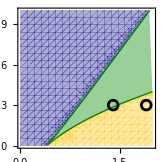

```mathematica
(*Clear[dy, db0, u, fileCplotUlo, CplotUlo]
(* Save the time-consuming steps as intermediate data files and use these files if they exist. *)
u=1;
fileCplotUlo = "data/Coexist-plot-u"  <> ToString[u] <> ".mx";
(* Takes ~3.2 min if file isn't saved *)
If[FileExistsQ[fileCplotUlo],
CplotUlo = Import[fileCplotUlo];, 
CplotUlo = RegionPlot[10^-8 < eqYprop[par1, par2, u]< (1 - 10^-8),{par1,0,2},{par2,0,1}, (*PlotLabel -> "u=1",*)
PlotPoints->30,
BoundaryStyle -> RGBColor["#008B00"], 
PlotStyle -> Directive[RGBColor["#008B00"], Opacity[0.4]]];
Export[fileCplotUlo,CplotUlo];];
CplotUlo*)

u=1;
p = coexistPlot[YplotUlo, BplotUlo, {{1.4,0.3}, {1.9, 0.3}}]
Export[File["2patch-u"  <> ToString[u] <> "-equilibria.pdf"],p];
Clear[p];
```

## Equilibria with u = 4

### Create separate plot objects:

```mathematica
Clear[dy, db0, u, fileYplotUhi, YplotUhi, fileBplotUhi, BplotUhi]
(* Save the time-consuming steps as intermediate data files and use these files if they exist. *)

u = 4;

fileYplotUhi = "data/Yplot-u"  <> ToString[u] <> ".mx";
fileBplotUhi = "data/Bplot-u" <> ToString[u] <> ".mx";


(* Takes ~1 min if file isn't saved *)
If[FileExistsQ[fileYplotUhi],
YplotUhi = Import[fileYplotUhi];, 
YplotUhi = RegionPlot[eqYprop[par1, par2, u] > (1 - 10^-8),{par1,0,2},{par2,0,1}, 
(*PlotLabel -> "u=" <> ToString[u],*)
BoundaryStyle-> Directive[RGBColor["#FFCC33"], Opacity[0.0]],
PlotStyle -> Directive[RGBColor["#FFCC33"], Opacity[0.4]]];
Export[fileYplotUhi,YplotUhi];];

(* Takes ~1.5 min if file isn't saved *)
If[FileExistsQ[fileBplotUhi],
BplotUhi = Import[fileBplotUhi];, 
BplotUhi = RegionPlot[10^-8 > eqYprop[par1, par2, u],{par1,0,2},{par2,0,1}, (*PlotLabel -> "u=" <> ToString[u],*)
BoundaryStyle-> Directive[RGBColor["#333399"], Opacity[0.0]],
PlotStyle -> Directive[RGBColor["#333399"], Opacity[0.4]]];
Export[fileBplotUhi,BplotUhi];];
```

### Combine to create final plot:

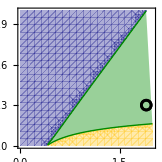

```mathematica
u = 4;
p = coexistPlot[YplotUhi, BplotUhi, {{1.9, 0.3}}]
Export[File["2patch-u" <> ToString[u] <> "-equilibria.pdf"],p];
Clear[p];
```

## Adding points to an equilibrium plot for specific outcomes

This is used in plots of community metrics for stochastic simulations where we vary the pollinator-dependent dispersal for yeast (d_yp) such that at u = 1 and no stochasticity, three different competitive outcomes occur.

{0.886308,1.17755,1.46879}

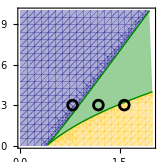

```mathematica
(* Find x for the point along a polygon's bounds where y is a certain value (x here being d_yp, y being d_b0, polygons define certain outcomes of competition): *)
getCoordPoint[coords_, yval : (_?NumericQ): 0.3 ] := Module[{pt1, pt2, b0, b1}, 
pt1 = Select[coords, Abs[#[[2]] - yval] == Min[Abs[Select[Map[#[[2]] &, coords], # < yval&] - yval]] &][[1]];
pt2 = Select[coords, Abs[#[[2]] - yval] == Min[Abs[Select[Map[#[[2]] &, coords], # > yval&] - yval]] &][[1]];
b1 = (pt2[[2]] - pt1[[2]]) / (pt2[[1]] - pt1[[1]]);
b0 = pt1[[2]] - b1 * pt1[[1]];
(yval - b0) / b1];
Bwins = getCoordPoint[getCoords[BplotUlo]];
Ywins = getCoordPoint[getCoords[YplotUlo]];
BYcoexist = (Bwins + Ywins)/2;
{Bwins, BYcoexist, Ywins}
ptsToAdd = {{Bwins - 0.1,0.3}, {BYcoexist, 0.3}, {Ywins+0.1, 0.3}};

u = 1;
p = coexistPlot[YplotUlo, BplotUlo, ptsToAdd]
Export[File["2patch-u" <> ToString[u] <> "-equilibria-extra-pts.pdf"],p];
Clear[p];
Clear[Bwins, BYcoexist, Ywins, ptsToAdd]
```